```mathematica
Clear["Global`*"];
```

```mathematica
(* Импортируем данные из файла *)
Data1=Import[NotebookDirectory[]<>"Continuous1.dat"][[2;;]];
Data2=Import[NotebookDirectory[]<>"Continuous1.dat"][[2;;]];
Data={Data1,Data2};
SubDir="tmp";
```

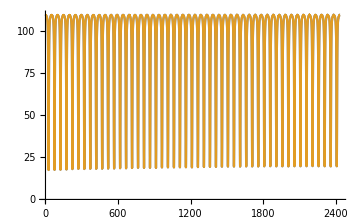
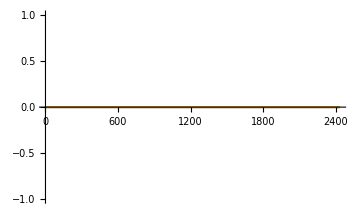

```mathematica
(* Смотрим на графики фазы и её погрешности в процентах в зависимости от времени в минутах *)
{ListPlot[{Transpose[{Data[[1,All,12]],Data[[1,All,6]]}],Transpose[{Data[[2,All,12]],Data[[2,All,6]]}]},PlotRange->All, Joined->True,ImageSize->Medium],
ListPlot[{Transpose[{Data[[1,All,12]],Data[[1,All,7]]}],Transpose[{Data[[2,All,12]],Data[[2,All,7]]}]},PlotRange->All, Joined->True,ImageSize->Medium]}
```

```mathematica
(* Вбиваем параметры эксперимента и резонанса, которые скрипту сложно определить автоматически *)
To= {87300,87300};
Kprt = {-6.3582,-6.2703};
(* Определяем необходимые функции и значения параметров, которые программа может вычислить сама *)
Temperature[i_,Fres_, F0_] := N[(Fres-F0)/Kprt[[i]]];
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;
gaussian[y0_,A_,μ_, σ_, x_] := y0 + A/(σ Sqrt[Pi/2])×Exp[(-2(x-μ)^2)/σ^2];
lorenz[y0_,A_,μ_, σ_, x_]:=y0 + (2A)/Pi×σ/(4 (x-μ)^2+σ^2);
linear[A_,B_,x_] := A x+B;
L = {Length[Data1[[All,1]]],Length[Data2[[All,1]]]};
From = {Data1[[1,3]],Data2[[1,3]]};
Step = {Data1[[2,3]]- Data1[[1,3]],Data2[[2,3]]- Data2[[1,3]]};
RoundLength = Ceiling[N[(To-From+1)/Step]];
(*RoundLength[[2]]=RoundLength[[2]]+1;*)
FullRounds = Floor[N[L/RoundLength]];
```

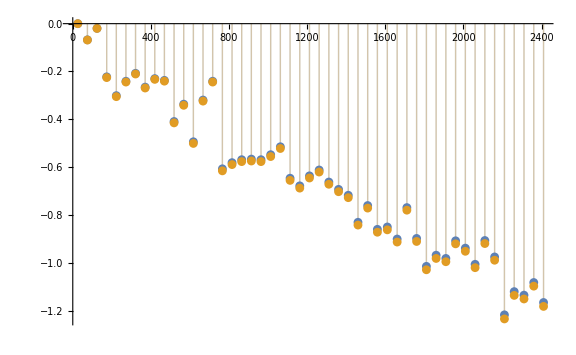

```mathematica
(KineticsMin=Table[
KineticsMinDataset= Table[
MinTheta = Min[Data[[i,All,6]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]]];
MinThetaIndex = Position[Data[[i,All,6]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]],MinTheta][[1,1]];
If[Length[MinThetaIndex]>0,MinThetaIndex=MinThetaIndex[[1]]];
Fres=Data[[i,All,1]][[(round-1)×RoundLength[[i]]+MinThetaIndex]];
Ffirst = Switch[round==1,True,Fres,False, Ffirst];
Temp = Temperature[i,Fres,Ffirst];
Time = (Data[[i,All,12]][[(round-1)×RoundLength[[i]] + MinThetaIndex]]);
{Time,Temp},{round,1,FullRounds[[i]]}];
KineticsMinDataset,{i,1,Length[Data]}])//TableForm;
ListPlot[KineticsMin,PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis]
```

```mathematica
(* Строим зависимость температуры от времени, ориентируясь на минимальное аппроксимацию измеренных данных в каждом раунде *)
Off[NonlinearModelFit::sszero]
(KineticsFit=Table[
KineticsFitDataset= Table[
RoundData = Transpose[{
Data[[i,All,1]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]],
Data[[i,All,6]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]]
}];
PhaseMin=Min[RoundData[[All,2]]];
If[Length[PhaseMin]>0,PhaseMin=PhaseMin[[1]]];
PhaseMax=Max[RoundData[[All,2]]];
If[Length[PhaseMax]>0,PhaseMax=PhaseMax[[1]]];
σ0 = Length[Select[RoundData,PhaseMin≤#[[2]]≤PhaseMin+(PhaseMax-PhaseMin)/2&]];
(* Аппроксимация параболой, где выбираются точки по фазе от минимума до четвертьвысоты *)
RoundDataParaboloid =Select[RoundData,(0.5×From[[i]]≤#[[1]]≤2×To[[i]])&&(PhaseMin≤#[[2]]≤PhaseMin+(PhaseMax-PhaseMin)/4)&] ;
nlmRoundParaboloid = NonlinearModelFit[
RoundDataParaboloid,paraboloid[y0,A,μ,t],
{{y0,Max[RoundDataParaboloid[[All,2]]]},
{A,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 2]][[1]]},
{μ,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 1]][[1]]}},
t];
parametersTableRoundParaboloid = nlmRoundParaboloid["ParameterTable"];
FresParaboloid = parametersTableRoundParaboloid[[1,1,4,2]];
FfirstParaboloid = Switch[round==1,True,FresParaboloid,False, FfirstParaboloid];
TempParaboloid = Temperature[i,FresParaboloid,FfirstParaboloid];
(* Аппроксимация гауссом *)
nlmRoundGaussian = NonlinearModelFit[
RoundData,gaussian[y0,A,μ,σ,t],
{{y0,Max[RoundData[[All,2]]]},
{A,σ0×RoundData[[Ordering[RoundData[[All, 2]],1], 2]][[1]]},
{μ,RoundData[[Ordering[RoundData[[All, 2]],1], 1]][[1]]}, 
{σ,σ0}},
t];
parametersTableRoundGaussian = nlmRoundGaussian["ParameterTable"];
FresGaussian = parametersTableRoundGaussian[[1,1,4,2]];
FfirstGaussian = Switch[round==1,True,FresGaussian,False, FfirstGaussian];
TempGaussian = Temperature[i,FresGaussian,FfirstGaussian];
(* Аппроксимация лоренцом *)
nlmRoundLorenz = NonlinearModelFit[
RoundData,lorenz[y0,A,μ,σ,t],
{{y0,Max[RoundData[[All,2]]]},
{A,σ0×RoundData[[Ordering[RoundData[[All, 2]],1], 2]][[1]]},
{μ,RoundData[[Ordering[RoundData[[All, 2]],1], 1]][[1]]}, 
{σ,σ0}},
t];
parametersTableRoundLorenz = nlmRoundLorenz["ParameterTable"];
FresLorenz = parametersTableRoundLorenz[[1,1,4,2]];
FfirstLorenz = Switch[round==1,True,FresLorenz,False, FfirstLorenz];
TempLorenz = Temperature[i,FresLorenz,FfirstLorenz];
(* Экспорт и отображение *)
(*Export[NotebookDirectory[]<>SubDir<>"\\"<>ToString[i]<>"_"<>"Round"<>ToString[round]<>".png",
Show[
ListPlot[RoundData,PlotRange->All, Joined->False,ImageSize->Large,Filling->None],

Plot[paraboloid[parametersTableRoundParaboloid [[1,1,2,2]],parametersTableRoundParaboloid [[1,1,3,2]],parametersTableRoundParaboloid [[1,1,4,2]],t],{t,RoundDataParaboloid[[1,1]],RoundDataParaboloid[[-1,1]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Red]],Plot[gaussian[parametersTableRoundGaussian[[1,1,2,2]],parametersTableRoundGaussian[[1,1,3,2]],parametersTableRoundGaussian[[1,1,4,2]],parametersTableRoundGaussian[[1,1,5,2]],t],{t,Min[RoundData[[All,1]]],Max[RoundData[[All,1]]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Green]],
Plot[lorenz[parametersTableRoundLorenz[[1,1,2,2]],parametersTableRoundLorenz[[1,1,3,2]],parametersTableRoundLorenz[[1,1,4,2]],parametersTableRoundLorenz[[1,1,5,2]],t],{t,Min[RoundData[[All,1]]],Max[RoundData[[All,1]]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Yellow]]
]
];*)
(* Вычисление аппроксимации завивисимости частоты от времени *)
FreqTemperatureData = Transpose[{
Data[[i,All,1]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]],
Data[[i,All,12]][[(round-1)×RoundLength[[i]]+1;;round×RoundLength[[i]]]]
}];
nlmFreqTemp= NonlinearModelFit[FreqTemperatureData,linear[A,B,x],{{A,1},{B,1}},x];
parametersTableFreqTemp = nlmFreqTemp["ParameterTable"];
TimeParaboloid = linear[parametersTableFreqTemp[[1,1,2,2]],parametersTableFreqTemp[[1,1,3,2]],FresParaboloid];
TimeGaussian = linear[parametersTableFreqTemp[[1,1,2,2]],parametersTableFreqTemp[[1,1,3,2]],FresGaussian];
TimeLorenz = linear[parametersTableFreqTemp[[1,1,2,2]],parametersTableFreqTemp[[1,1,3,2]],FresLorenz];{round,TimeParaboloid,TempParaboloid,TimeGaussian,TempGaussian,TimeLorenz,TempLorenz,
parametersTableRoundGaussian[[1,1,2,2]], 100×Abs[parametersTableRoundGaussian[[1,1,2,3]]/parametersTableRoundGaussian[[1,1,2,2]]],(* Subscript[y, 0] Paraboloid, Subscript[δy, 0] Paraboloid *)
parametersTableRoundGaussian[[1,1,2,2]], 100×Abs[parametersTableRoundGaussian[[1,1,2,3]]/parametersTableRoundGaussian[[1,1,2,2]]],(* Subscript[y, 0] Gaussian, Subscript[δy, 0] Gaussian *)
parametersTableRoundGaussian[[1,1,3,2]], 100×Abs[parametersTableRoundGaussian[[1,1,3,3]]/parametersTableRoundGaussian[[1,1,3,2]]],(* AGaussian, δAGaussian *)
parametersTableRoundGaussian[[1,1,4,2]], 100×Abs[parametersTableRoundGaussian[[1,1,4,3]]/parametersTableRoundGaussian[[1,1,4,2]]],(* μGaussian, δμGaussian *)
parametersTableRoundGaussian[[1,1,5,2]], 100×Abs[parametersTableRoundGaussian[[1,1,5,3]]/parametersTableRoundGaussian[[1,1,5,2]]],(* σGaussian, δσGaussian *)
parametersTableRoundGaussian[[1,1,3,2]]/(parametersTableRoundGaussian[[1,1,5,2]]×Sqrt[Pi/2]),100×Sqrt[(parametersTableRoundGaussian[[1,1,3,3]]/parametersTableRoundGaussian[[1,1,3,2]])^2+(parametersTableRoundGaussian[[1,1,5,3]]/parametersTableRoundGaussian[[1,1,5,2]])^2],(* DeepGaussian, δDeepGaussian *)
parametersTableRoundLorenz[[1,1,2,2]], 100×Abs[parametersTableRoundLorenz[[1,1,2,3]]/parametersTableRoundLorenz[[1,1,2,2]]],(* Subscript[y, 0] Lorenz, Subscript[δy, 0] Lorenz *)
parametersTableRoundLorenz[[1,1,3,2]], 100×Abs[parametersTableRoundLorenz[[1,1,3,3]]/parametersTableRoundLorenz[[1,1,3,2]]],(* ALorenz, δALorenz *)
parametersTableRoundLorenz[[1,1,4,2]], 100×Abs[parametersTableRoundLorenz[[1,1,4,3]]/parametersTableRoundLorenz[[1,1,4,2]]],(* μLorenz, δμLorenz *)
parametersTableRoundLorenz[[1,1,5,2]], 100×Abs[parametersTableRoundLorenz[[1,1,5,3]]/parametersTableRoundLorenz[[1,1,5,2]]],(* σLorenz, δσLorenz *)
parametersTableRoundLorenz[[1,1,3,2]]/parametersTableRoundLorenz[[1,1,5,2]]×2/Pi,
100×Sqrt[(parametersTableRoundLorenz[[1,1,3,3]]/parametersTableRoundLorenz[[1,1,3,2]])^2+(parametersTableRoundLorenz[[1,1,5,3]]/parametersTableRoundLorenz[[1,1,5,2]])^2] (* DeepLorenz, δDeepLorenz *)

},
{round,1,FullRounds[[i]]}];
KineticsFitDataset,{i,1,Length[Data]}])//TableForm;
```

```mathematica
Off[DeleteFile::fdnfnd];
For[i=1,i≤Length[Data],i=i+1,
KineticsFitExport=Insert[KineticsFit[[i]],{"NRound[N]","TimeParabolic[m]","dTemperatureParabolic[C]","TimeGaussian[m]","dTemperatureGaussian[C]","TimeLorenz[m]","dTemperatureLorenz[C]","Y0Parabolic","dY0Parabolic[%]","Y0Gaussian","dY0Gaussian[%]","AGaussian","dAGaussian[%]","MuGaussian","dMuGaussian[%]","SigmaGaussian","dSigmaGaussian[%]","DeepGaussian[degree]","dDeepGaussian[%]","Y0Lorenz","dY0Lorenz[%]","ALorenz","dALorenz[%]","MuLorenz","dMuLorenz[%]","SigmaLorenz","dSigmaLorenz[%]","DeepLorenz[degree]","dDeepLorenz[%]"},1];
Export[NotebookDirectory[]<>ToString[i]<>"_KineticsFit.dat",Transpose[{KineticsFitExport[[All,2]],KineticsFitExport[[All,3]]}]];
DeleteFile[NotebookDirectory[]<>ToString[i]<>"_KineticsFit.fit"];
RenameFile[NotebookDirectory[]<>ToString[i]<>"_KineticsFit.dat",NotebookDirectory[]<>ToString[i]<>"_KineticsFit.fit"];
Export[NotebookDirectory[]<>ToString[i]<>"_dFres[Hz]FromT[m],Kprt[HzToK]="<>ToString[Kprt[[i]]]<>".xlsx",Transpose[{KineticsFitExport[[2;;,2]],Kprt[[i]]×KineticsFitExport[[2;;,3]]}]];
Export[NotebookDirectory[]<>ToString[i]<>"_AllDataKineticsFit,Kprt[HzToK]="<>ToString[Kprt[[i]]]<>".xlsx",KineticsFitExport];
];
```

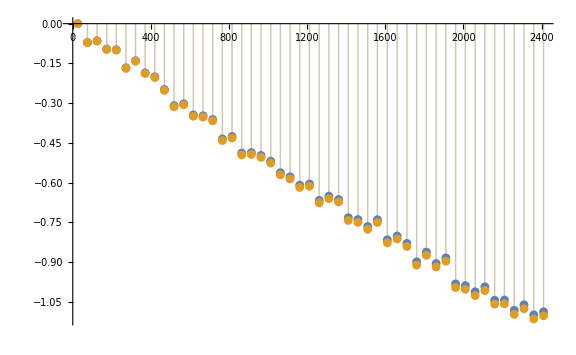

```mathematica
PlotKineticsFres = ListPlot[Table[Transpose[{KineticsFit[[i,All,2]],Kprt[[i]]×KineticsFit[[i,All,3]]}],{i,1,Length[Data]}],PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis];
Export[NotebookDirectory[]<>"dFres[Hz]FromT[m],Kprt[HzToK]="<>ToString[Kprt]<>".png",PlotKineticsFres];
PlotKineticsT = ListPlot[Table[Transpose[{KineticsFit[[i,All,2]],KineticsFit[[i,All,3]]}],{i,1,Length[Data]}],PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis]
Export[NotebookDirectory[]<>"dT[C]FromT[m],Kprt[HzToK]="<>ToString[Kprt]<>".png",PlotKineticsT];
```

```mathematica
PlotKineticsT = ListPlot[Table[Transpose[{KineticsFit[[i,;;10,2]],KineticsFit[[i,;;10,3]]}],{i,1,Length[Data]}],PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis];
```

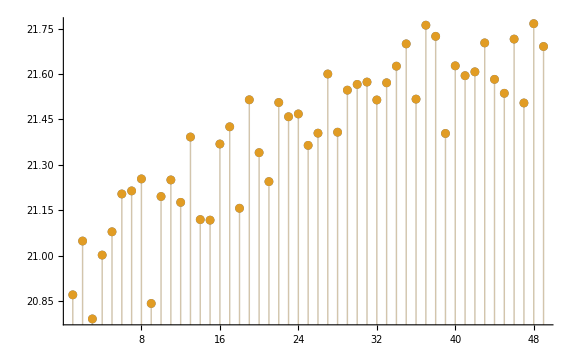

```mathematica
PlotKineticsT = ListPlot[Table[Transpose[{KineticsFit[[i,;;,1]],KineticsFit[[i,;;,26]]}],{i,1,Length[Data]}],PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis]
```

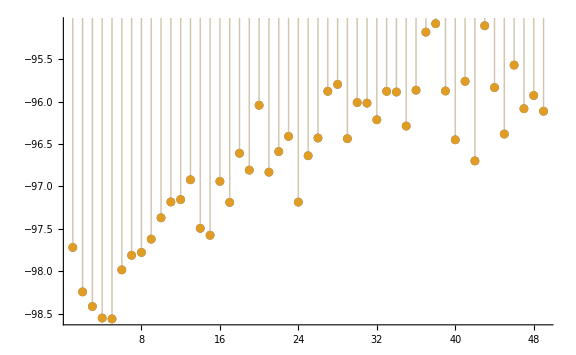

```mathematica
PlotKineticsT = ListPlot[Table[Transpose[{KineticsFit[[i,;;,1]],KineticsFit[[i,;;,28]]}],{i,1,Length[Data]}],PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis]
```